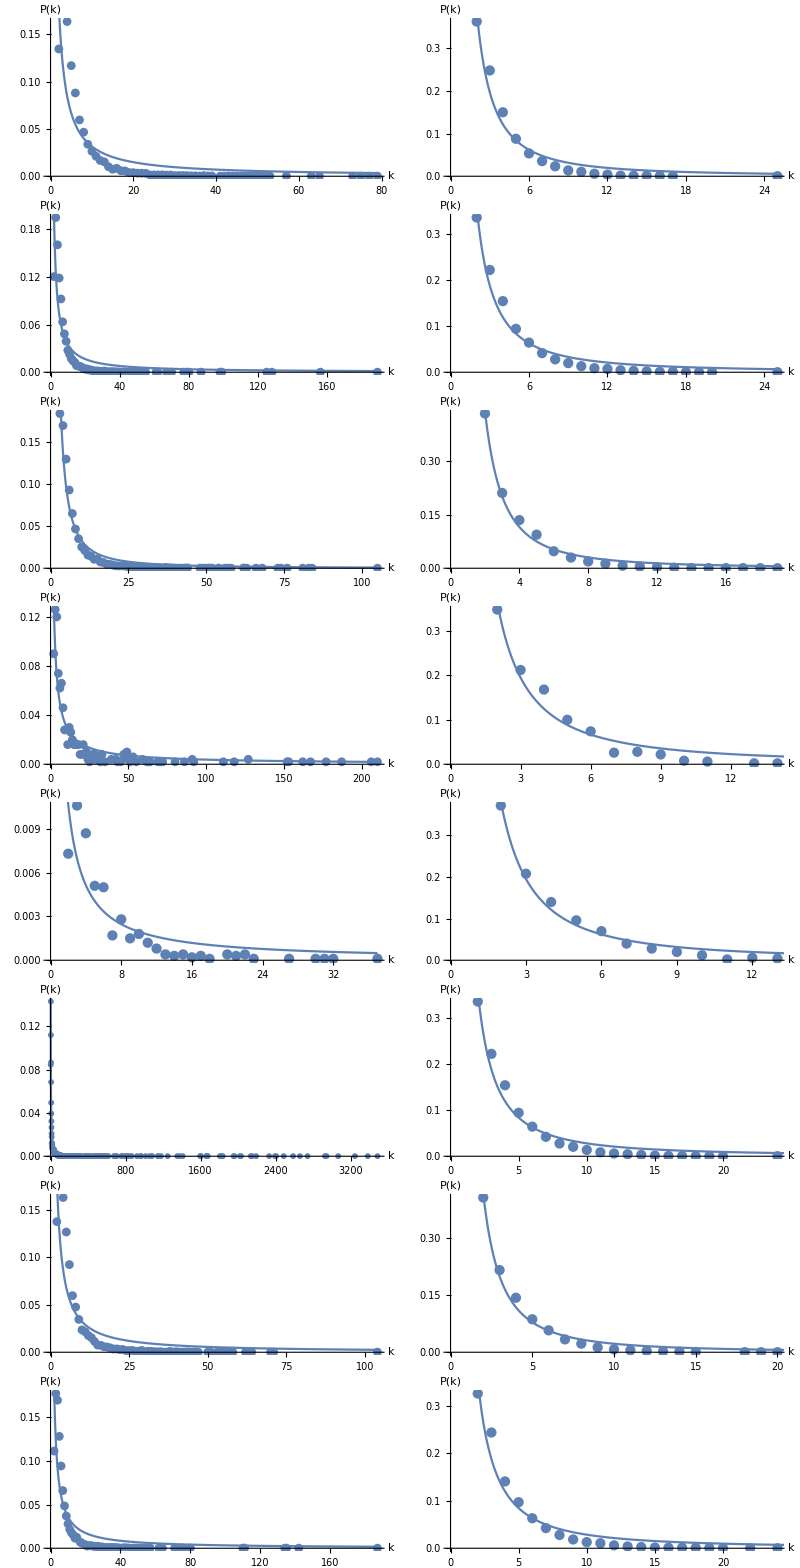
```mathematica
frame=-Graphics-;
```

```mathematica
visibility = frame[[1,All,1]];
```

```mathematica
horizontal = frame[[1,All,2]];
```

```mathematica
visibilityPoints=Cases[#,Point[data_]:>data,-4,1][[1]]&/@visibility;
```

```mathematica
horizontalPoints=Cases[#,Point[data_]:>data,-4,1][[1]]&/@horizontal;
```

### Add 10-primes

```mathematica
AppendTo[visibilityPoints,{{2,1325/9999},{5,1247/9999},{3,1985/9999},{7,598/9999},{13,14/909},{19,14/3333},{4,1619/9999},{9,359/9999},{8,469/9999},{11,71/3333},{6,844/9999},{17,62/9999},{18,6/1111},{25,14/9999},{15,106/9999},{10,82/3333},{14,127/9999},{31,13/9999},{12,58/3333},{23,7/3333},{22,28/9999},{24,17/9999},{61,1/9999},{26,19/9999},{16,76/9999},{37,5/9999},{21,32/9999},{43,2/9999},{46,4/9999},{48,4/9999},{73,1/9999},{28,5/3333},{33,4/3333},{29,5/9999},{20,41/9999},{27,10/9999},{30,8/9999},{39,5/9999},{38,5/9999},{36,7/9999},{35,1/3333},{34,4/9999},{32,4/9999},{40,1/3333},{45,1/9999},{53,2/9999},{60,2/9999},{74,1/9999},{65,1/9999},{87,1/9999},{42,1/3333},{47,1/9999},{57,1/9999},{44,1/9999},{54,1/9999}}];
```

```mathematica
AppendTo[horizontalPoints,{{2,3493/9999},{4,1490/9999},{3,766/3333},{5,29/303},{6,607/9999},{7,4/99},{8,259/9999},{9,170/9999},{11,7/909},{12,38/9999},{13,7/3333},{14,17/9999},{15,2/1111},{17,4/9999},{10,127/9999},{16,1/1111},{20,4/9999},{18,1/3333},{19,1/9999}}];
```

### Add 11-primes

```mathematica
AppendTo[visibilityPoints,{{181,4/9999},{182,1/1111},{184,1/9999},{172,1/9999},{162,1/9999},{160,2/9999},{289,1/9999},{111,8/9999},{117,14/9999},{114,7/9999},{120,7/9999},{115,8/9999},{123,4/9999},{112,1/909},{107,2/3333},{294,1/9999},{96,1/909},{100,4/3333},{110,7/9999},{94,1/909},{106,5/9999},{109,2/3333},{113,1/1111},{116,1/3333},{118,7/9999},{325,2/9999},{98,7/9999},{95,1/909},{105,1/1111},{103,8/9999},{92,2/3333},{259,1/9999},{102,8/9999},{350,1/9999},{99,7/9999},{97,1/1111},{108,4/3333},{104,2/3333},{93,5/9999},{101,5/9999},{127,5/9999},{384,1/9999},{79,14/9999},{64,14/9999},{84,14/9999},{71,25/9999},{82,14/9999},{54,14/3333},{67,26/9999},{57,1/303},{56,4/1111},{53,53/9999},{698,1/9999},{47,70/9999},{59,29/9999},{38,158/9999},{943,1/9999},{58,4/1111},{39,131/9999},{66,20/9999},{55,38/9999},{76,2/909},{69,16/9999},{63,2/1111},{41,10/909},{78,7/9999},{868,1/9999},{34,131/9999},{50,20/3333},{46,65/9999},{51,20/3333},{36,19/1111},{1389,1/9999},{75,23/9999},{33,124/9999},{35,50/3333},{37,175/9999},{44,10/1111},{45,20/3333},{1728,1/9999},{1634,1/9999},{40,131/9999},{30,89/9999},{8,287/9999},{5,19/303},{25,1/303},{12,164/9999},{11,65/3333},{31,29/3333},{6,500/9999},{26,5/1111},{20,94/9999},{16,35/3333},{3,1024/9999},{4,745/9999},{10,82/3333},{19,70/9999},{23,2/303},{21,82/9999},{15,107/9999},{14,10/909},{17,91/9999},{2,199/3333},{2293,1/9999},{48,23/3333},{22,23/3333},{18,32/3333},{13,13/1111},{9,83/3333},{7,41/1111},{24,16/3333},{29,71/9999},{28,82/9999},{164,1/9999},{187,1/9999},{183,4/9999},{179,1/9999},{190,2/9999},{177,1/9999},{186,1/9999},{188,1/9999},{195,1/9999},{175,1/9999},{171,1/9999},{255,1/3333},{231,2/9999},{169,1/9999},{81,19/9999},{453,1/9999},{193,1/9999},{90,16/9999},{88,2/9999},{91,4/3333},{280,1/9999},{62,25/9999},{254,2/9999},{89,1/1111},{77,1/909},{455,1/9999},{83,4/3333},{60,2/909},{52,49/9999},{85,1/1111},{86,5/3333},{119,2/3333},{87,8/9999},{74,2/909},{121,2/9999},{359,2/9999},{625,1/9999},{602,1/9999},{65,23/9999},{32,85/9999},{200,1/9999},{207,1/9999},{209,1/9999},{140,1/3333},{72,19/9999},{70,2/909},{122,5/9999},{73,17/9999},{42,94/9999},{68,20/9999},{221,1/9999},{138,4/9999},{61,20/9999},{735,1/9999},{1766,1/9999},{135,2/9999},{139,1/3333},{49,59/9999},{658,1/9999},{134,4/9999},{131,2/9999},{409,1/9999},{498,1/9999},{366,1/9999},{487,1/9999},{508,1/9999},{533,1/9999},{407,1/9999},{480,1/9999},{422,1/9999},{512,1/9999},{559,1/9999},{490,1/9999},{563,1/9999},{303,1/9999},{143,1/3333},{146,1/9999},{465,1/9999},{592,1/9999},{348,1/9999},{206,1/9999},{320,1/9999},{201,1/9999},{212,2/9999},{214,1/9999},{942,1/9999},{643,1/9999},{220,1/9999},{232,1/9999},{448,1/9999},{328,1/9999},{125,2/9999},{851,1/9999},{1400,1/9999},{803,1/9999},{154,1/3333},{241,1/9999},{43,82/9999},{155,2/9999},{129,4/9999},{784,1/9999},{266,1/9999},{80,17/9999},{599,1/9999},{128,4/9999},{130,1/3333},{397,1/9999},{751,1/9999},{152,1/9999},{1130,1/9999},{203,1/9999},{793,2/9999},{1343,1/9999},{665,1/9999},{238,1/9999},{543,1/9999},{415,1/9999},{669,1/9999},{202,1/9999},{996,1/9999},{204,1/9999},{1015,1/9999},{824,2/9999},{389,1/9999},{249,1/9999},{940,1/9999},{132,1/9999},{133,1/9999},{855,1/9999},{1553,1/9999},{151,2/9999},{347,1/9999},{198,1/9999},{774,1/9999},{1068,1/9999},{649,1/9999},{240,1/9999},{351,1/9999},{383,1/9999},{136,1/9999},{491,1/9999},{659,1/9999},{230,2/9999},{1612,1/9999},{235,1/9999},{1157,1/9999},{147,2/9999},{194,1/9999},{159,1/9999},{148,1/9999},{1477,1/9999},{1348,1/9999},{145,1/3333},{124,2/9999},{156,1/9999},{229,1/9999},{126,1/9999},{1920,1/9999},{1203,1/9999},{27,53/9999},{1670,1/9999},{1153,1/9999},{1223,1/9999},{1336,1/9999},{153,1/3333},{1542,1/9999},{375,1/9999},{191,1/9999},{349,1/9999},{144,1/9999},{1083,1/9999},{520,1/9999},{142,1/9999},{982,1/9999},{1485,1/9999},{948,1/9999},{199,2/9999},{2307,1/9999},{1429,1/9999},{1494,1/9999},{944,1/9999},{1740,1/9999},{1806,1/9999},{1148,1/9999},{936,1/9999},{1921,1/9999},{150,1/9999},{1759,2/9999},{2348,1/9999},{1973,1/9999},{2125,1/9999},{2410,1/9999},{2343,1/9999},{2070,1/9999},{1885,1/9999},{2474,1/9999},{2347,1/9999},{211,1/9999},{137,2/9999},{700,1/9999},{2175,1/9999},{1387,1/9999},{2315,1/9999},{1720,1/9999},{1915,1/9999},{1587,1/9999},{2094,1/9999},{958,1/9999},{1819,1/9999},{2266,1/9999},{1258,1/9999},{1708,2/9999},{1648,2/9999},{2145,1/9999},{1599,1/9999},{1419,1/9999},{1651,1/9999},{1799,1/9999},{1772,1/9999},{1659,1/9999},{766,1/9999},{1894,1/9999},{1770,1/9999},{1661,1/9999},{1471,1/9999},{1562,1/9999},{1705,1/9999},{1726,1/9999},{224,1/9999},{1567,1/9999},{189,1/9999},{1908,1/9999},{1180,1/9999},{1686,1/9999},{2144,1/9999},{2451,1/9999},{1660,1/9999},{1675,1/9999},{1919,1/9999},{1787,1/9999},{1752,1/9999},{1559,1/9999},{1848,1/9999},{1711,1/9999},{1769,1/9999},{1546,1/9999},{1667,1/9999},{1665,1/9999},{1853,1/9999},{1715,1/9999},{1589,1/9999},{1603,1/9999},{1706,1/9999}}];
```

```mathematica
AppendTo[horizontalPoints,{{2,179/500},{3,111/500},{5,21/250},{4,93/500},{6,19/250},{8,13/500},{9,1/100},{7,3/125},{10,1/250},{11,1/250},{12,1/500}}];
```

### Add 12-primes

```mathematica
AppendTo[visibilityPoints,{{3,1762/9999},{6,103/1111},{11,217/9999},{4,565/3333},{8,475/9999},{20,53/9999},{2,13/101},{5,416/3333},{13,40/3333},{14,38/3333},{10,289/9999},{17,7/1111},{18,5/1111},{28,2/1111},{7,227/3333},{16,62/9999},{9,332/9999},{19,43/9999},{25,3/1111},{37,1/3333},{12,173/9999},{27,2/1111},{44,1/3333},{15,1/99},{31,7/9999},{59,2/9999},{36,5/9999},{32,8/9999},{21,37/9999},{46,1/9999},{58,2/9999},{121,1/9999},{35,5/9999},{29,1/1111},{30,1/1111},{24,19/9999},{22,38/9999},{23,25/9999},{26,2/1111},{34,1/1111},{52,1/9999},{40,4/9999},{39,1/909},{41,4/9999},{38,2/9999},{62,2/9999},{54,1/9999},{50,2/9999},{45,1/9999},{33,5/9999},{49,4/9999},{55,1/9999},{42,2/9999},{60,2/9999},{98,1/9999},{89,1/9999},{47,1/9999},{53,1/9999},{51,1/9999}}];
```

```mathematica
AppendTo[horizontalPoints,{{3,2174/9999},{7,4/99},{4,1451/9999},{9,53/3333},{2,413/1111},{5,961/9999},{6,571/9999},{10,12/1111},{11,25/3333},{8,260/9999},{13,35/9999},{14,7/3333},{12,37/9999},{16,2/3333},{15,8/9999},{17,5/9999},{24,1/9999},{19,1/3333},{18,1/9999}}];
```

### Add 13-primes

```mathematica
AppendTo[visibilityPoints,{{269,1/1111},{177,2/3333},{179,2/3333},{268,7/9999},{416,1/9999},{470,1/9999},{267,5/9999},{476,1/9999},{494,2/9999},{492,1/9999},{485,1/9999},{265,1/9999},{507,1/9999},{550,1/9999},{556,1/9999},{531,1/9999},{270,1/9999},{570,1/9999},{484,1/9999},{566,1/9999},{546,1/9999},{271,2/9999},{588,1/9999},{273,2/9999},{581,1/9999},{584,1/9999},{274,2/9999},{603,1/9999},{266,2/9999},{609,1/9999},{578,1/9999},{623,2/9999},{278,1/3333},{276,1/9999},{649,1/9999},{282,1/9999},{283,1/9999},{644,1/9999},{264,1/9999},{279,1/9999},{281,2/9999},{617,1/9999},{290,1/3333},{660,1/9999},{289,2/9999},{690,1/9999},{286,1/9999},{291,1/9999},{297,2/9999},{704,1/9999},{300,1/9999},{683,1/9999},{304,1/9999},{280,1/9999},{727,1/9999},{305,1/9999},{312,1/9999},{307,1/9999},{316,1/9999},{709,1/9999},{217,5/9999},{320,1/9999},{748,1/9999},{315,2/9999},{318,2/9999},{319,2/9999},{759,1/9999},{335,1/9999},{331,1/9999},{336,1/9999},{334,1/9999},{764,1/9999},{347,1/9999},{342,1/9999},{343,1/9999},{309,1/9999},{337,1/9999},{768,1/9999},{338,1/9999},{359,1/9999},{371,1/9999},{346,1/9999},{373,1/9999},{786,1/9999},{403,1/9999},{808,1/9999},{311,1/9999},{339,1/9999},{365,1/9999},{396,1/9999},{801,1/9999},{412,1/9999},{425,1/9999},{411,1/9999},{851,1/9999},{432,1/9999},{455,1/9999},{364,1/9999},{445,1/9999},{443,2/9999},{861,1/9999},{192,7/9999},{818,1/9999},{911,1/9999},{366,1/9999},{921,1/9999},{429,1/9999},{916,1/9999},{943,1/9999},{974,1/9999},{992,1/9999},{923,1/9999},{968,1/9999},{984,1/9999},{1071,1/9999},{1078,1/9999},{1076,1/9999},{1079,1/9999},{1123,1/9999},{1120,1/9999},{1105,1/9999},{1143,1/9999},{1188,1/9999},{1212,1/9999},{1270,1/9999},{1216,1/9999},{1238,1/9999},{1156,1/9999},{1237,1/9999},{1314,1/9999},{1312,1/9999},{1356,1/9999},{1285,1/9999},{1322,1/9999},{1341,1/9999},{1378,1/9999},{1515,1/9999},{1516,1/9999},{893,1/9999},{1559,1/9999},{1542,1/9999},{1562,1/9999},{1605,1/9999},{1658,1/9999},{1652,1/9999},{1722,1/9999},{1812,1/9999},{1814,1/9999},{1813,1/9999},{1871,1/9999},{1869,1/9999},{1922,1/9999},{1908,1/9999},{1910,1/9999},{1911,1/9999},{1933,1/9999},{2001,2/9999},{2074,1/9999},{2163,1/9999},{2150,1/9999},{2156,1/9999},{2159,1/9999},{2310,1/9999},{2261,1/9999},{2320,1/9999},{2399,1/9999},{2643,1/9999},{2747,1/9999},{2767,1/9999},{1612,1/9999},{2661,1/9999},{2855,1/9999},{2809,1/9999},{2862,1/9999},{2909,1/9999},{3043,1/9999},{3066,1/9999},{2969,1/9999},{3241,1/9999},{3275,1/9999},{3311,1/9999},{1299,1/9999},{3267,1/9999},{3486,1/9999},{3476,1/9999},{3559,1/9999},{3585,1/9999},{3613,1/9999},{3579,1/9999},{3628,1/9999},{3649,1/9999},{3565,1/9999},{3652,1/9999},{3822,1/9999},{3808,1/9999},{3869,1/9999},{3910,1/9999},{4101,1/9999},{4095,1/9999},{3997,1/9999},{4121,1/9999},{4138,1/9999},{4182,1/9999},{4211,1/9999},{4244,1/9999},{4264,1/9999},{4207,1/9999},{4226,1/9999},{4359,1/9999},{4402,1/9999},{4462,1/9999},{4567,1/9999},{975,1/9999},{4552,1/9999},{4556,1/9999},{4232,1/9999},{4633,1/9999},{4764,1/9999},{4900,1/9999},{2773,1/9999},{4877,1/9999},{4953,1/9999},{4955,1/9999},{5210,1/9999},{5300,1/9999},{4982,1/9999},{5493,1/9999},{5473,1/9999},{5756,1/9999},{4467,1/9999},{5655,1/9999},{5910,1/9999},{5804,1/9999},{5292,1/9999},{6204,1/9999},{6360,1/9999},{173,1/1111},{185,8/9999},{182,5/9999},{181,8/9999},{180,7/9999},{170,14/9999},{258,1/9999},{169,1/1111},{176,8/9999},{254,1/9999},{183,4/3333},{178,2/3333},{186,1/3333},{251,1/9999},{248,1/9999},{245,2/9999},{242,1/9999},{175,5/9999},{238,1/3333},{239,1/9999},{167,13/9999},{172,4/9999},{236,2/9999},{237,1/9999},{233,1/9999},{235,2/9999},{231,2/9999},{171,8/9999},{232,1/9999},{230,1/9999},{164,7/9999},{226,2/9999},{161,8/9999},{168,7/9999},{224,2/9999},{223,1/9999},{222,1/3333},{225,1/3333},{165,5/9999},{220,2/9999},{163,1/1111},{158,5/9999},{218,4/9999},{219,2/9999},{166,5/9999},{162,8/9999},{157,8/9999},{216,2/9999},{215,2/9999},{208,2/3333},{212,1/3333},{211,1/9999},{214,2/9999},{204,2/9999},{155,4/3333},{209,1/9999},{207,5/9999},{160,1/3333},{201,1/3333},{203,1/9999},{154,4/3333},{205,2/9999},{202,1/9999},{196,8/9999},{156,4/3333},{149,10/9999},{199,2/9999},{197,5/9999},{198,4/9999},{150,5/3333},{194,8/9999},{193,1/3333},{152,1/909},{151,4/3333},{195,1/3333},{191,1/3333},{190,8/9999},{148,10/9999},{189,2/3333},{187,1/1111},{146,20/9999},{159,1/3333},{153,10/9999},{188,4/9999},{184,7/9999},{144,1/1111},{147,4/9999},{145,1/1111},{143,2/1111},{142,23/9999},{140,14/9999},{141,13/9999},{174,2/9999},{139,13/9999},{120,2/1111},{132,19/9999},{131,14/9999},{124,2/1111},{119,16/9999},{122,13/9999},{134,13/9999},{129,4/3333},{121,20/9999},{133,14/9999},{138,16/9999},{137,2/1111},{128,5/3333},{125,19/9999},{135,3/1111},{126,13/9999},{136,20/9999},{127,16/9999},{116,25/9999},{118,19/9999},{123,2/3333},{117,14/9999},{114,23/9999},{130,7/9999},{115,19/9999},{108,25/9999},{111,19/9999},{110,5/3333},{113,10/9999},{112,5/3333},{109,2/1111},{101,37/9999},{105,7/3333},{107,8/3333},{102,37/9999},{103,2/909},{90,25/9999},{99,28/9999},{97,10/3333},{92,35/9999},{106,8/3333},{94,28/9999},{93,26/9999},{104,5/3333},{91,34/9999},{100,28/9999},{98,20/9999},{95,41/9999},{88,2/909},{96,31/9999},{89,28/9999},{87,2/909},{83,10/3333},{82,10/3333},{85,29/9999},{81,4/909},{79,46/9999},{86,20/9999},{77,50/9999},{80,46/9999},{84,20/9999},{78,43/9999},{70,86/9999},{76,43/9999},{73,19/3333},{74,64/9999},{71,10/1111},{75,6/1111},{69,8/1111},{72,58/9999},{68,13/3333},{62,58/9999},{64,35/9999},{66,34/9999},{67,38/9999},{65,1/303},{61,64/9999},{63,62/9999},{59,50/9999},{60,49/9999},{58,58/9999},{57,5/909},{56,17/3333},{53,17/3333},{55,32/9999},{52,40/9999},{49,31/9999},{50,28/9999},{43,61/9999},{48,10/3333},{41,6/1111},{54,56/9999},{47,50/9999},{51,26/9999},{42,43/9999},{44,4/909},{45,34/9999},{46,10/3333},{39,14/3333},{40,62/9999},{37,1/303},{35,34/9999},{30,1/303},{36,32/9999},{28,53/9999},{33,10/3333},{20,95/9999},{34,13/3333},{38,2/909},{26,4/909},{32,31/9999},{31,1/303},{27,6/1111},{29,41/9999},{23,20/3333},{19,25/3333},{25,16/3333},{21,7/909},{22,9/1111},{24,56/9999},{16,12/1111},{17,79/9999},{18,8/1111},{13,127/9999},{12,146/9999},{15,119/9999},{14,136/9999},{11,161/9999},{9,20/909},{10,184/9999},{4,62/909},{7,310/9999},{8,239/9999},{5,523/9999},{6,127/3333},{3,866/9999},{2,170/3333}}];
```

```mathematica
AppendTo[horizontalPoints,{{2,3364/9999},{5,934/9999},{4,1552/9999},{6,646/9999},{3,2227/9999},{9,193/9999},{7,142/3333},{8,284/9999},{10,145/9999},{11,28/3333},{12,67/9999},{13,4/1111},{15,13/9999},{14,19/9999},{16,1/3333},{19,1/9999},{18,1/9999},{20,1/9999},{22,1/9999},{17,1/9999}}];
```

### Add 14-primes

```mathematica
AppendTo[visibilityPoints,{{2,1339/9999},{7,686/9999},{5,1165/9999},{9,362/9999},{21,29/9999},{8,427/9999},{3,1933/9999},{4,185/1111},{6,874/9999},{20,38/9999},{29,4/3333},{11,67/3333},{23,2/1111},{18,62/9999},{15,29/3333},{13,146/9999},{17,23/3333},{28,5/3333},{36,4/9999},{12,169/9999},{35,8/9999},{69,1/9999},{22,32/9999},{14,13/1111},{25,5/3333},{10,30/1111},{24,10/3333},{16,82/9999},{19,40/9999},{40,4/9999},{32,10/9999},{38,2/3333},{31,8/9999},{49,4/9999},{61,1/9999},{100,1/9999},{30,1/1111},{26,1/909},{43,1/3333},{39,2/9999},{27,10/9999},{45,2/9999},{37,7/9999},{41,2/9999},{33,5/9999},{34,1/9999},{66,1/9999},{46,1/9999},{42,4/9999},{76,1/9999},{62,1/9999},{64,2/9999},{57,1/9999},{47,2/9999},{60,1/9999},{48,1/9999},{44,1/9999}}];
```

```mathematica
AppendTo[horizontalPoints,{{2,3571/9999},{5,931/9999},{3,2350/9999},{9,53/3333},{4,1505/9999},{7,376/9999},{6,193/3333},{12,16/3333},{10,32/3333},{8,79/3333},{13,28/9999},{14,14/9999},{11,79/9999},{15,4/3333},{16,1/9999},{18,5/9999},{17,4/9999},{19,1/9999},{24,1/9999}}];
```

### Add 15-primes

```mathematica
AppendTo[visibilityPoints,{{83,2/9999},{80,2/9999},{66,17/9999},{52,1/303},{79,1/3333},{45,14/3333},{89,4/9999},{65,17/9999},{93,1/9999},{61,10/9999},{70,8/9999},{95,1/9999},{71,5/9999},{99,1/9999},{98,2/9999},{126,1/9999},{168,1/9999},{142,2/9999},{206,1/9999},{118,1/9999},{261,1/9999},{85,2/9999},{229,1/9999},{86,4/9999},{90,1/9999},{100,1/9999},{120,1/9999},{108,1/9999},{264,1/9999},{114,1/9999},{276,1/9999},{310,1/9999},{293,1/9999},{384,1/9999},{410,1/9999},{437,1/9999},{182,1/9999},{213,1/9999},{341,1/9999},{477,1/9999},{482,1/9999},{577,1/9999},{568,1/9999},{513,1/9999},{197,1/9999},{131,1/9999},{475,1/9999},{536,2/9999},{595,1/9999},{648,1/9999},{736,1/9999},{709,1/9999},{746,1/9999},{94,1/9999},{787,1/9999},{205,1/9999},{724,1/9999},{844,1/9999},{923,1/9999},{968,1/9999},{976,1/9999},{1006,1/9999},{1004,1/9999},{1017,1/9999},{1038,1/9999},{1073,1/9999},{1179,1/9999},{1240,1/9999},{1207,1/9999},{1224,1/9999},{1414,1/9999},{1488,1/9999},{1551,1/9999},{1601,1/9999},{520,1/9999},{1682,1/9999},{1687,1/9999},{1738,1/9999},{1876,1/9999},{1913,1/9999},{1933,1/9999},{1987,1/9999},{2054,1/9999},{2142,1/9999},{2231,1/9999},{2276,1/9999},{51,2/909},{48,8/3333},{46,26/9999},{81,1/3333},{82,4/9999},{77,2/3333},{54,4/3333},{41,20/9999},{78,5/9999},{53,8/3333},{50,1/303},{39,10/3333},{76,2/9999},{37,10/3333},{69,4/3333},{67,4/3333},{73,1/3333},{60,7/9999},{58,16/9999},{49,8/3333},{43,20/9999},{75,1/9999},{44,28/9999},{63,4/3333},{72,5/9999},{47,20/9999},{56,17/9999},{62,1/1111},{68,5/9999},{64,14/9999},{74,5/9999},{38,16/3333},{55,2/1111},{34,37/9999},{59,5/3333},{57,13/9999},{40,19/9999},{32,47/9999},{36,38/9999},{31,16/3333},{84,2/9999},{92,1/9999},{33,32/9999},{30,37/9999},{35,31/9999},{29,4/1111},{42,20/9999},{25,53/9999},{28,13/3333},{27,25/9999},{19,10/1111},{22,8/1111},{26,52/9999},{20,29/3333},{21,80/9999},{23,67/9999},{17,107/9999},{15,38/3333},{24,7/1111},{18,115/9999},{16,35/3333},{13,17/1111},{14,13/1111},{8,415/9999},{12,62/3333},{10,30/1111},{7,194/3333},{9,331/9999},{11,7/303},{6,8/101},{5,1030/9999},{4,1354/9999},{3,161/1111},{2,82/909}}];
```

```mathematica
AppendTo[horizontalPoints,{{2,3365/9999},{5,103/1111},{4,1558/9999},{6,653/9999},{3,2227/9999},{8,284/9999},{7,428/9999},{10,146/9999},{9,191/9999},{12,59/9999},{11,89/9999},{13,37/9999},{14,5/3333},{15,10/9999},{16,5/9999},{19,1/9999},{18,1/9999},{20,1/9999},{21,1/9999}}];
```

### Add 16-primes

```mathematica
AppendTo[visibilityPoints,{{3,207/1111},{5,443/3333},{8,41/909},{9,358/9999},{39,5/9999},{17,73/9999},{2,1241/9999},{7,208/3333},{4,1673/9999},{12,185/9999},{10,296/9999},{25,16/9999},{6,899/9999},{15,76/9999},{11,65/3333},{20,40/9999},{23,1/303},{14,11/909},{30,10/9999},{13,41/3333},{46,1/3333},{57,1/9999},{32,7/9999},{72,2/9999},{121,1/9999},{16,83/9999},{19,14/3333},{21,34/9999},{24,13/9999},{22,29/9999},{42,5/9999},{27,7/9999},{26,2/909},{40,2/9999},{44,1/9999},{31,8/9999},{18,6/1111},{28,13/9999},{36,2/3333},{45,1/3333},{35,4/9999},{67,2/9999},{29,10/9999},{33,2/3333},{38,2/3333},{64,1/9999},{37,7/9999},{54,1/9999},{63,1/9999},{56,2/9999},{51,2/9999},{59,2/9999},{68,1/9999},{48,1/9999},{34,2/9999},{43,1/9999},{50,1/9999},{47,1/9999},{41,1/9999}}];
```

```mathematica
AppendTo[horizontalPoints,{{2,1241/3333},{3,2239/9999},{7,134/3333},{6,571/9999},{4,159/1111},{9,50/3333},{8,268/9999},{12,4/909},{11,62/9999},{5,920/9999},{10,112/9999},{15,5/3333},{20,1/3333},{18,5/9999},{14,16/9999},{13,8/3333},{16,8/9999},{21,1/3333},{17,1/9999},{19,2/9999}}];
```

## Plots

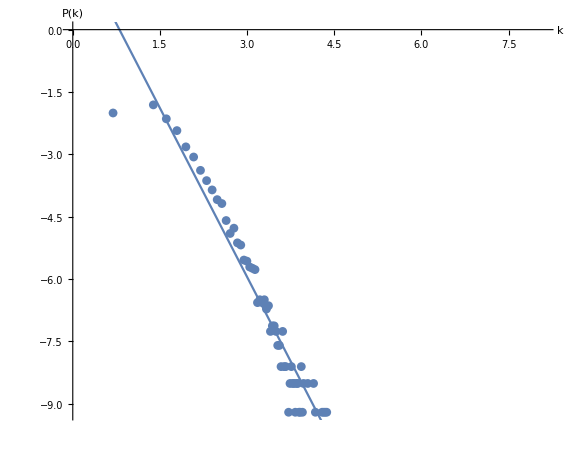
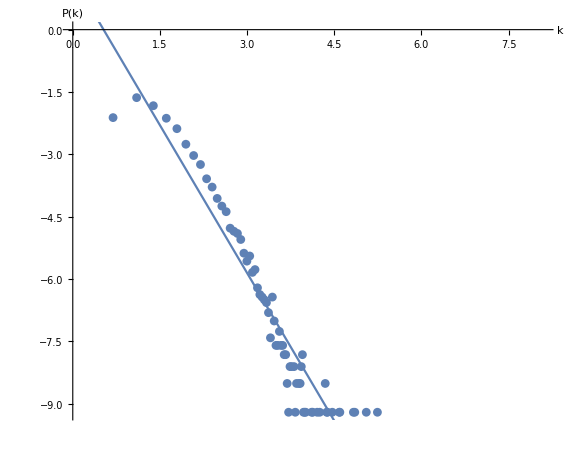
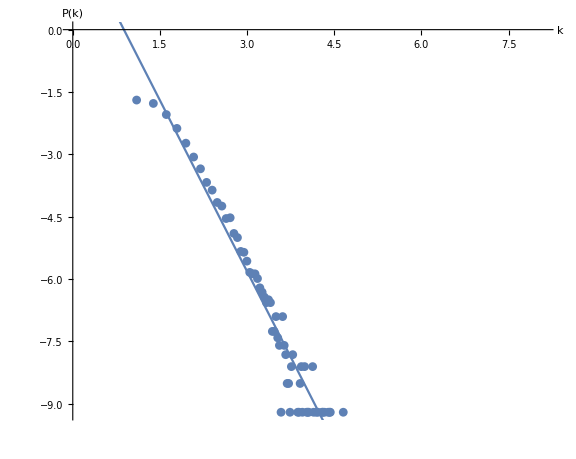
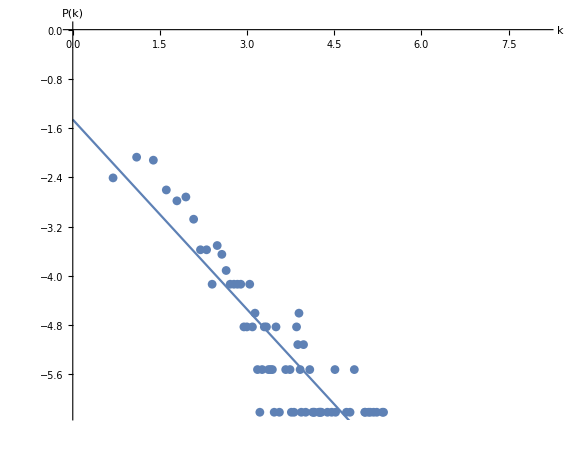
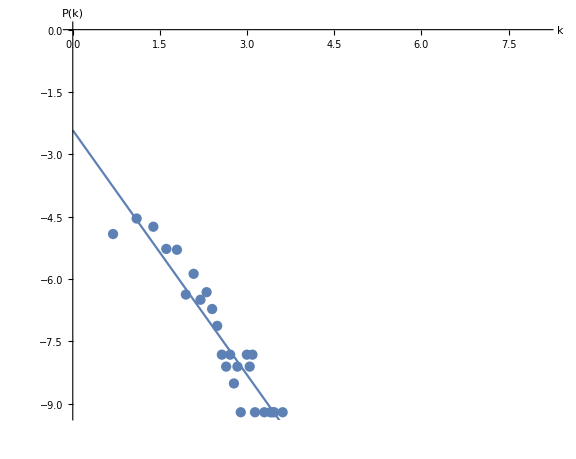
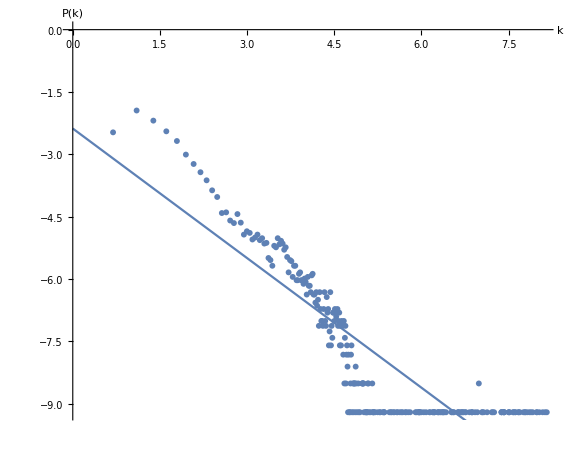
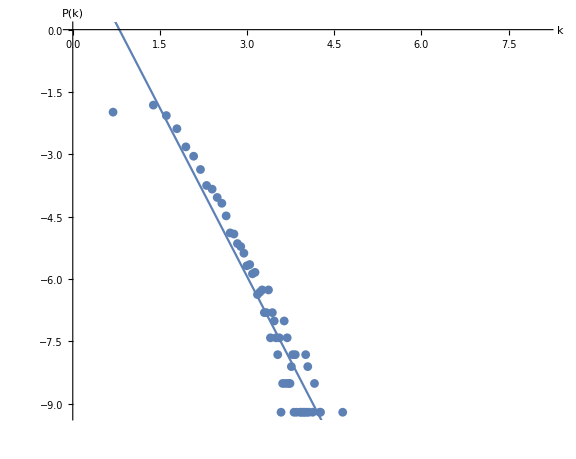
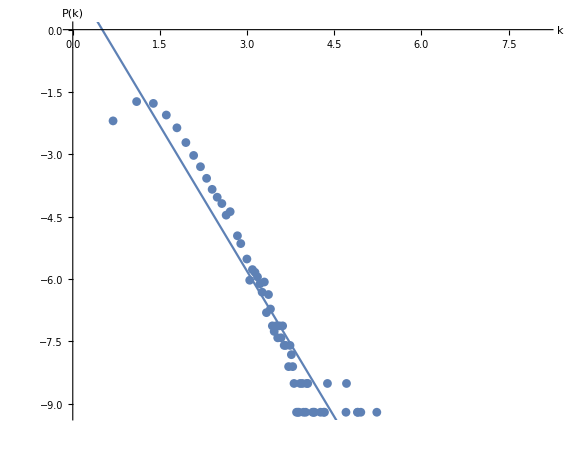
{-Graphics-d=2,-Graphics-d=3,-Graphics-d=4,-Graphics-d=5,-Graphics-d=6,-Graphics-d=7,-Graphics-d=8,-Graphics-d=9,-Graphics-d=10,-Graphics-d=11,-Graphics-d=12,-Graphics-d=13,-Graphics-d=14,-Graphics-d=15,-Graphics-d=16}

```mathematica
visibilityPlots=(
lm=LinearModelFit[Log@#[[1]],x,x];
Labeled[Show[
ListPlot[Log@#[[1]],PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
Plot[lm[x],{x,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large,AspectRatio->0.8
],Style[#[[2]],38],Top])&/@Transpose@{visibilityPoints,{"d=2","d=3","d=4","d=5","d=6","d=7","d=8","d=9","d=10","d=11","d=12","d=13","d=14","d=15","d=16"}}
```

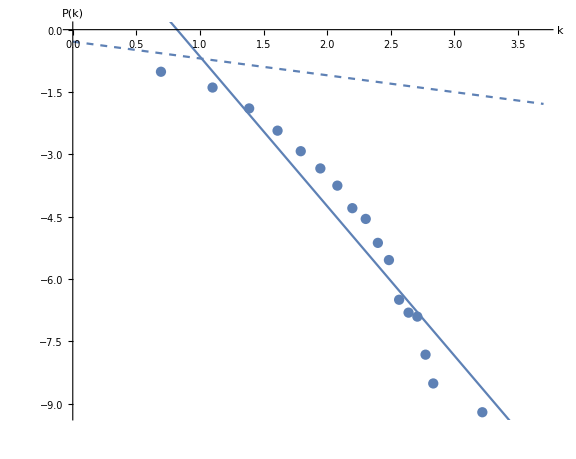
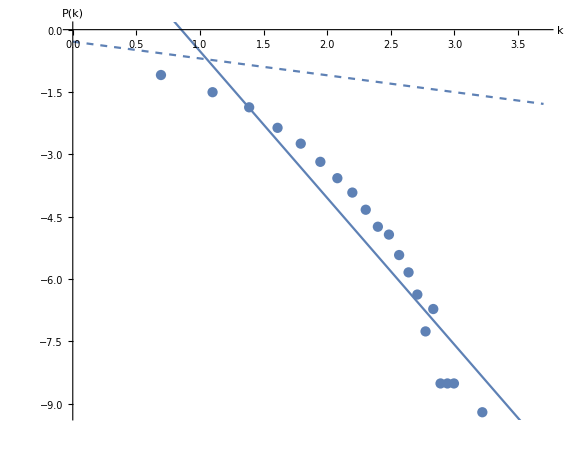
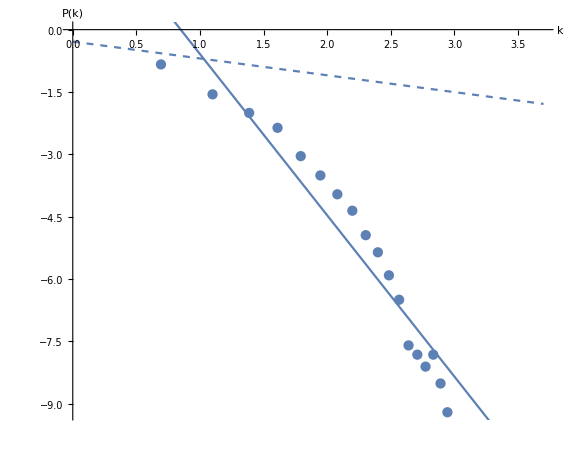
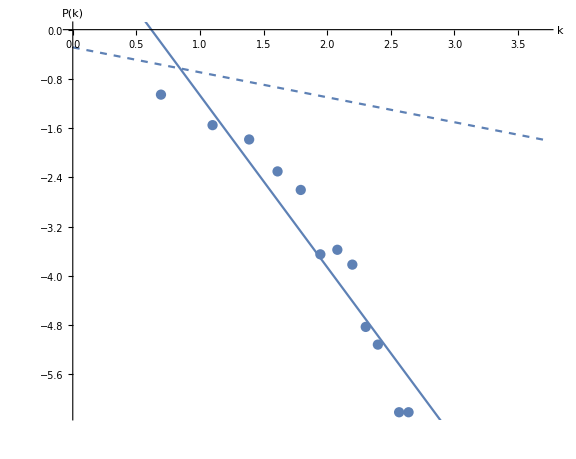
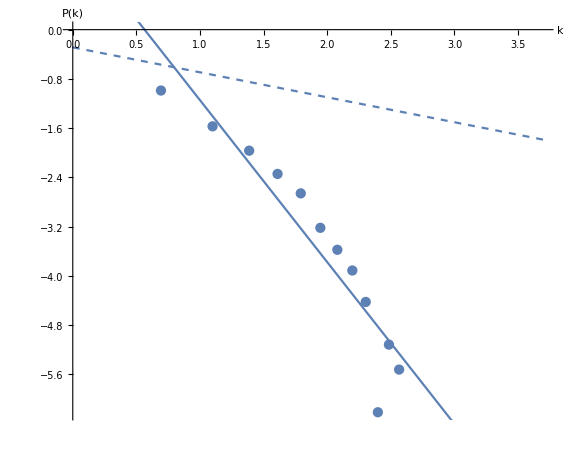
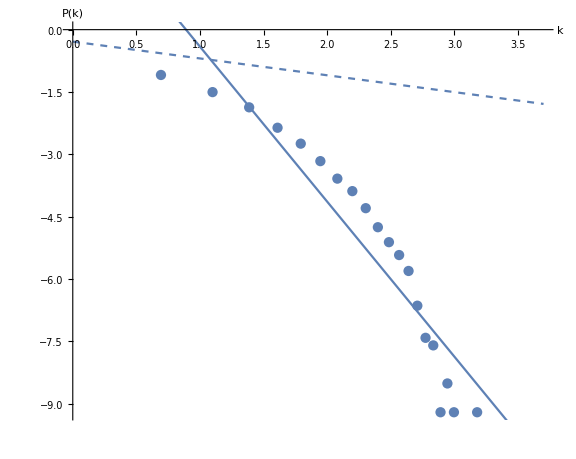
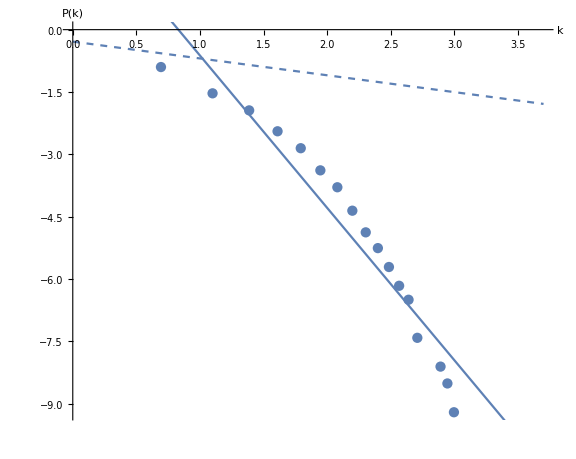
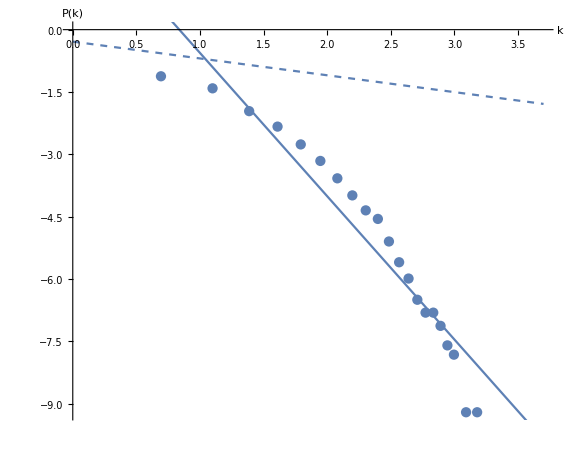
{-Graphics-d=2,-Graphics-d=3,-Graphics-d=4,-Graphics-d=5,-Graphics-d=6,-Graphics-d=7,-Graphics-d=8,-Graphics-d=9,-Graphics-d=10,-Graphics-d=11,-Graphics-d=12,-Graphics-d=13,-Graphics-d=14,-Graphics-d=15,-Graphics-d=16}

```mathematica
horizontalPlots=(
lm=LinearModelFit[Log@#[[1]],x,x];
fm=1/3(2/3)^(#-2)&;
Labeled[Show[
ListPlot[Log@#[[1]],PlotRange->{{0,3.7},All},AxesOrigin->{0,0}],
Plot[lm[x],{x,0,3.7},PlotRange->{{0,3.7},All},AxesOrigin->{0,0}],
Plot[Log@fm[x],{x,0,3.7},PlotRange->{{0,3.7},All},AxesOrigin->{0,0},PlotStyle->Dashed],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large,AspectRatio->0.8
],Style[#[[2]],38],Top])&/@Transpose@{horizontalPoints,{"d=2","d=3","d=4","d=5","d=6","d=7","d=8","d=9","d=10","d=11","d=12","d=13","d=14","d=15","d=16"}}
```

```mathematica
Export["natural-2.eps",visibilityPlots[[1]]];
Export["horizontal-2.eps",horizontalPlots[[1]]];
Export["naturalGrid.eps", Grid[Partition[visibilityPlots,3],Spacings->{Automatic,4}]];
Export["horizontalGrid.eps", Grid[Partition[horizontalPlots,3],Spacings->{Automatic,4}]];
```

## d = 10

### visibility

```mathematica
countrel={{2,1325/9999},{5,1247/9999},{3,1985/9999},{7,598/9999},{13,14/909},{19,14/3333},{4,1619/9999},{9,359/9999},{8,469/9999},{11,71/3333},{6,844/9999},{17,62/9999},{18,6/1111},{25,14/9999},{15,106/9999},{10,82/3333},{14,127/9999},{31,13/9999},{12,58/3333},{23,7/3333},{22,28/9999},{24,17/9999},{61,1/9999},{26,19/9999},{16,76/9999},{37,5/9999},{21,32/9999},{43,2/9999},{46,4/9999},{48,4/9999},{73,1/9999},{28,5/3333},{33,4/3333},{29,5/9999},{20,41/9999},{27,10/9999},{30,8/9999},{39,5/9999},{38,5/9999},{36,7/9999},{35,1/3333},{34,4/9999},{32,4/9999},{40,1/3333},{45,1/9999},{53,2/9999},{60,2/9999},{74,1/9999},{65,1/9999},{87,1/9999},{42,1/3333},{47,1/9999},{57,1/9999},{44,1/9999},{54,1/9999}};
```

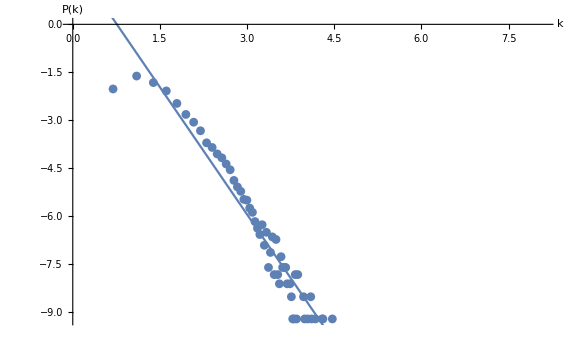

```mathematica
(lm=LinearModelFit[Log@#,x,x];
Show[
ListPlot[Log@#,PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
Plot[lm[x],{x,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
])&@countrel
```

```mathematica
results={};
```

```mathematica
degree=VertexDegree[igv10]//Mean//N
```

6.23062

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.438508/x^1.09623]

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

```mathematica
results
```

{{visibility,10,9999,6.23062,1.09623 ± 0.187463,0.438508 ± 0.117337}}

```mathematica
Export["v10.eps",-Graphics-]
```

v10.eps

### horizontal visibility

```mathematica
countrel={{2,3493/9999},{4,1490/9999},{3,766/3333},{5,29/303},{6,607/9999},{7,4/99},{8,259/9999},{9,170/9999},{11,7/909},{12,38/9999},{13,7/3333},{14,17/9999},{15,2/1111},{17,4/9999},{10,127/9999},{16,1/1111},{20,4/9999},{18,1/3333},{19,1/9999}};
```

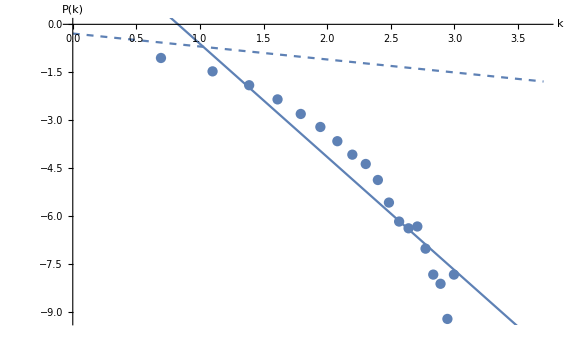

```mathematica
(
lm=LinearModelFit[Log@#,x,x];
fm=1/3(2/3)^(#-2)&;
Show[
ListPlot[Log@#,PlotRange->{{0,3.7},All},AxesOrigin->{0,0}],
Plot[lm[x],{x,0,3.7},PlotRange->{{0,3.7},All},AxesOrigin->{0,0}],
Plot[Log@fm[x],{x,0,3.7},PlotRange->{{0,3.7},All},AxesOrigin->{0,0},PlotStyle->Dashed],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
])&@countrel
```

```mathematica
Export["h10.eps",-Graphics-]
```

h10.eps

```mathematica
degree=VertexDegree[igh10]//Mean//N
```

3.84218

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.1457/x^1.62678]

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

```mathematica
results//TableForm
```

visibility | 10 | 9999 | 6.23062 | 1.09623 ± 0.187463 | 0.438508 ± 0.117337
visibility | 10 | 9999 | 3.84218 | 1.62678 ± 0.206643 | 1.1457 ± 0.237232

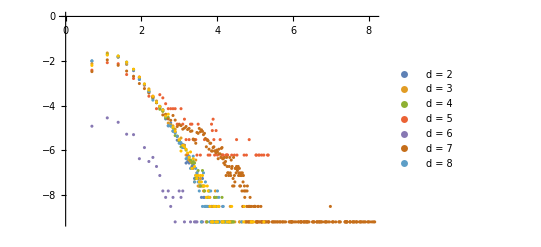

```mathematica
ListPlot[Log@visibilityPoints,PlotRange->{{0,8.1},All},AxesOrigin->{0,0},PlotLegends->{"d = 2","d = 3","d = 4","d = 5","d = 6","d = 7","d = 8"}]
```

```mathematica
lms=LinearModelFit[Log@#,x,x][y]&/@visibilityPoints
```

{2.1772-2.71055 y,1.25734-2.37216 y,2.4161-2.7461 y,-1.46055-1.02792 y,-2.42184-1.96406 y,-2.3801-1.03996 y,2.16589-2.70372 y,1.18409-2.33426 y}

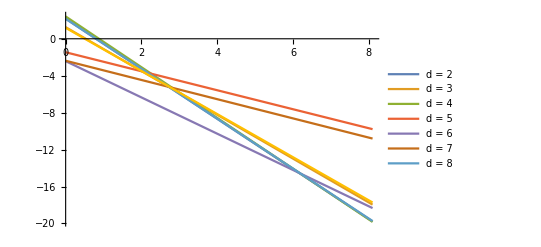

```mathematica
Plot[{2.1771995170383946-2.7105522658721974 y,1.2573403955105085-2.37216020084492 y,2.4161030852343557-2.7460957230348537 y,-1.460545067175454-1.0279248355706383 y,-2.421840496243267-1.9640589793665224 y,-2.3801019198021014-1.0399614466205362 y,2.16588703016536-2.703716924005051 y,1.18409246190788-2.3342645616459414 y},{y,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0},
PlotLegends->{"d = 2","d = 3","d = 4","d = 5","d = 6","d = 7","d = 8"}]
```

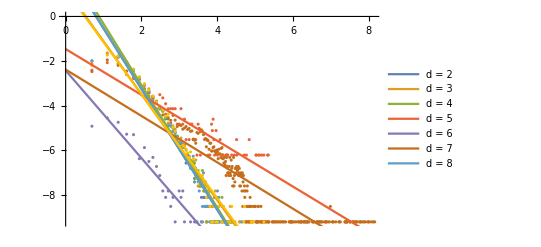

```mathematica
Show[
ListPlot[Log@visibilityPoints,PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
Plot[lms,{y,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0},
PlotLegends->{"d = 2","d = 3","d = 4","d = 5","d = 6","d = 7","d = 8"}]
]
```

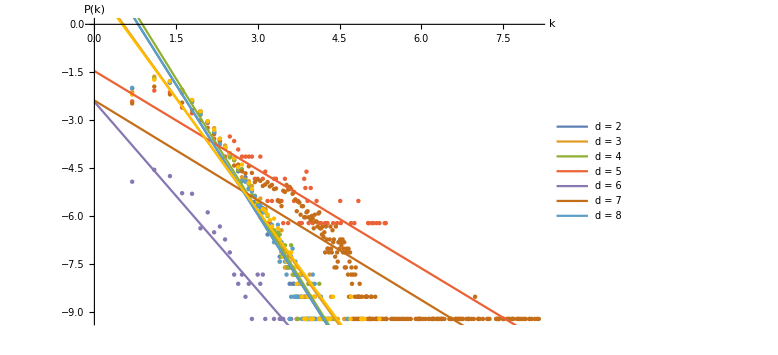

```mathematica
Show[
ListPlot[Log@visibilityPoints,PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
Plot[lms,{y,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0},
PlotLegends->{"d = 2","d = 3","d = 4","d = 5","d = 6","d = 7","d = 8"}]
,
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export["graph.pdf", %%]
```

graph.pdf

## d=11

```mathematica
visibilityPoints
```

{{{2.,0.134513},{5.,0.116912},{7.,0.059506},{12.,0.0167017},{23.,0.00310031},{4.,0.163516},{6.,0.0880088},{10.,0.0264026},{11.,0.0211021},{9.,0.0338034},{16.,0.00840084},{27.,0.00150015},{57.,0.00020002},{17.,0.00590059},{14.,0.010101},{8.,0.0466047},{26.,0.00140014},{13.,0.0152015},{15.,0.00740074},{19.,0.00390039},{20.,0.00380038},{29.,0.00130013},{18.,0.00560056},{22.,0.00320032},{37.,0.00070007},{31.,0.00080008},{33.,0.00070007},{48.,0.00020002},{53.,0.00020002},{73.,0.00010001},{79.,0.00010001},{21.,0.00330033},{24.,0.00140014},{28.,0.00120012},{32.,0.00080008},{30.,0.00070007},{38.,0.00030003},{36.,0.00030003},{25.,0.00150015},{34.,0.00050005},{45.,0.00020002},{63.,0.00020002},{44.,0.00020002},{51.,0.00030003},{77.,0.00010001},{65.,0.00010001},{49.,0.00010001},{75.,0.00010001},{39.,0.00030003},{43.,0.00030003},{35.,0.00050005},{41.,0.00010001},{46.,0.00010001},{47.,0.00020002},{42.,0.00020002},{50.,0.00010001},{52.,0.00010001}},{{31.,0.00160016},{30.,0.00060006},{28.,0.00140014},{26.,0.00160016},{23.,0.00310031},{29.,0.00110011},{24.,0.0020002},{27.,0.00150015},{21.,0.00430043},{20.,0.00380038},{32.,0.00090009},{43.,0.00030003},{36.,0.00050005},{37.,0.00050005},{52.,0.00040004},{53.,0.00010001},{49.,0.00020002},{98.,0.00010001},{50.,0.00020002},{47.,0.00020002},{70.,0.00010001},{79.,0.00010001},{99.,0.00010001},{87.,0.00010001},{77.,0.00020002},{125.,0.00010001},{156.,0.00010001},{128.,0.00010001},{189.,0.00010001},{22.,0.00290029},{15.,0.00840084},{19.,0.00460046},{10.,0.0276028},{6.,0.0922092},{14.,0.0125013},{12.,0.0172017},{8.,0.0483048},{9.,0.0389039},{4.,0.160316},{3.,0.194619},{18.,0.00640064},{2.,0.120312},{16.,0.00780078},{13.,0.0143014},{7.,0.0634063},{5.,0.118512},{17.,0.00740074},{11.,0.0226023},{39.,0.00040004},{42.,0.00030003},{33.,0.00050005},{25.,0.00170017},{35.,0.00070007},{34.,0.00050005},{38.,0.00040004},{40.,0.00020002},{45.,0.00030003},{61.,0.00010001},{62.,0.00010001},{80.,0.00010001},{67.,0.00010001},{51.,0.00030003},{54.,0.00010001},{55.,0.00010001},{41.,0.00010001},{46.,0.00010001}},{{4.,0.169317},{7.,0.0650065},{8.,0.0466047},{12.,0.0156016},{27.,0.00160016},{3.,0.183618},{5.,0.129513},{6.,0.0928093},{9.,0.0351035},{13.,0.0143014},{21.,0.00290029},{30.,0.00140014},{54.,0.00030003},{14.,0.0106011},{15.,0.0108011},{25.,0.0020002},{23.,0.00280028},{19.,0.00470047},{10.,0.0253025},{26.,0.00180018},{11.,0.0210021},{29.,0.00150015},{22.,0.00280028},{20.,0.00380038},{18.,0.00480048},{16.,0.00740074},{31.,0.00070007},{24.,0.00250025},{39.,0.00040004},{50.,0.00020002},{73.,0.00010001},{17.,0.00670067},{37.,0.0010001},{62.,0.00030003},{33.,0.0010001},{28.,0.00140014},{38.,0.00050005},{51.,0.00030003},{35.,0.00050005},{43.,0.00030003},{81.,0.00010001},{68.,0.00010001},{83.,0.00010001},{105.,0.00010001},{41.,0.00020002},{32.,0.00070007},{34.,0.00060006},{44.,0.00040004},{57.,0.00010001},{36.,0.00010001},{56.,0.00010001},{66.,0.00010001},{49.,0.00010001},{63.,0.00010001},{74.,0.00010001},{76.,0.00010001},{84.,0.00010001},{40.,0.00020002},{48.,0.00010001},{58.,0.00010001},{52.,0.00010001},{42.,0.00010001}},{{47.,0.008},{48.,0.006},{49.,0.01},{50.,0.004},{42.,0.004},{51.,0.002},{55.,0.002},{59.,0.004},{53.,0.006},{62.,0.002},{69.,0.002},{70.,0.002},{63.,0.002},{64.,0.002},{72.,0.002},{71.,0.002},{91.,0.004},{92.,0.002},{86.,0.002},{118.,0.002},{111.,0.002},{127.,0.004},{80.,0.002},{167.,0.002},{28.,0.008},{152.,0.002},{33.,0.008},{162.,0.002},{153.,0.002},{177.,0.002},{210.,0.002},{187.,0.002},{206.,0.002},{45.,0.002},{43.,0.002},{39.,0.004},{35.,0.002},{32.,0.002},{30.,0.004},{31.,0.004},{24.,0.004},{27.,0.008},{20.,0.008},{23.,0.01},{29.,0.004},{18.,0.016},{21.,0.016},{16.,0.016},{26.,0.004},{15.,0.016},{22.,0.008},{17.,0.016},{13.,0.026},{14.,0.02},{12.,0.03},{10.,0.028},{11.,0.016},{19.,0.008},{3.,0.126},{9.,0.028},{25.,0.002},{8.,0.046},{2.,0.09},{5.,0.074},{7.,0.066},{4.,0.12},{6.,0.062}},{{3.,0.0106011},{2.,0.00730073},{4.,0.00870087},{9.,0.00150015},{6.,0.0050005},{15.,0.00040004},{8.,0.00280028},{5.,0.00510051},{13.,0.00040004},{21.,0.00030003},{22.,0.00040004},{37.,0.00010001},{11.,0.00120012},{17.,0.00030003},{10.,0.00180018},{7.,0.00170017},{14.,0.00030003},{12.,0.00080008},{16.,0.00020002},{20.,0.00040004},{31.,0.00010001},{30.,0.00010001},{32.,0.00010001},{23.,0.00010001},{18.,0.00010001},{27.,0.00010001}},{{145.,0.00020002},{146.,0.00020002},{147.,0.00020002},{148.,0.00020002},{149.,0.00020002},{154.,0.00010001},{155.,0.00010001},{157.,0.00010001},{150.,0.00010001},{160.,0.00020002},{158.,0.00010001},{164.,0.00010001},{162.,0.00020002},{173.,0.00020002},{176.,0.00010001},{159.,0.00010001},{174.,0.00010001},{137.,0.00010001},{178.,0.00010001},{177.,0.00010001},{198.,0.00010001},{182.,0.00010001},{197.,0.00010001},{190.,0.00010001},{168.,0.00010001},{213.,0.00010001},{211.,0.00010001},{207.,0.00010001},{232.,0.00010001},{238.,0.00010001},{249.,0.00010001},{241.,0.00010001},{286.,0.00010001},{253.,0.00010001},{278.,0.00010001},{267.,0.00010001},{292.,0.00010001},{264.,0.00010001},{309.,0.00010001},{306.,0.00010001},{332.,0.00010001},{130.,0.00030003},{321.,0.00010001},{381.,0.00010001},{370.,0.00010001},{393.,0.00010001},{387.,0.00010001},{364.,0.00010001},{385.,0.00010001},{391.,0.00010001},{403.,0.00010001},{437.,0.00010001},{420.,0.00010001},{467.,0.00010001},{463.,0.00010001},{489.,0.00010001},{506.,0.00010001},{492.,0.00010001},{501.,0.00010001},{503.,0.00010001},{544.,0.00010001},{557.,0.00010001},{567.,0.00010001},{581.,0.00010001},{584.,0.00010001},{588.,0.00010001},{616.,0.00010001},{600.,0.00010001},{682.,0.00010001},{676.,0.00010001},{538.,0.00010001},{705.,0.00010001},{698.,0.00010001},{759.,0.00010001},{769.,0.00010001},{823.,0.00010001},{802.,0.00010001},{797.,0.00010001},{865.,0.00010001},{827.,0.00010001},{966.,0.00010001},{959.,0.00010001},{921.,0.00010001},{961.,0.00010001},{1014.,0.00010001},{854.,0.00010001},{1056.,0.00010001},{1144.,0.00010001},{1082.,0.00020002},{1148.,0.00010001},{115.,0.00040004},{1177.,0.00010001},{1248.,0.00010001},{1351.,0.00010001},{1408.,0.00010001},{1375.,0.00010001},{1661.,0.00010001},{1672.,0.00010001},{1603.,0.00010001},{1595.,0.00010001},{1600.,0.00010001},{1674.,0.00010001},{1805.,0.00010001},{1820.,0.00010001},{1952.,0.00010001},{1960.,0.00010001},{2030.,0.00010001},{1664.,0.00010001},{2018.,0.00010001},{2134.,0.00010001},{2148.,0.00010001},{2191.,0.00010001},{2404.,0.00010001},{533.,0.00010001},{755.,0.00010001},{2330.,0.00010001},{2392.,0.00010001},{2485.,0.00010001},{2585.,0.00010001},{2657.,0.00010001},{2739.,0.00010001},{212.,0.00010001},{2925.,0.00010001},{2941.,0.00010001},{3066.,0.00010001},{3244.,0.00010001},{1835.,0.00010001},{3381.,0.00010001},{3484.,0.00010001},{140.,0.00010001},{136.,0.00020002},{131.,0.00020002},{133.,0.00010001},{127.,0.00020002},{129.,0.00010001},{126.,0.00020002},{125.,0.00010001},{121.,0.00050005},{124.,0.00020002},{128.,0.00020002},{118.,0.00010001},{122.,0.00010001},{120.,0.00040004},{112.,0.00050005},{119.,0.00020002},{117.,0.00010001},{113.,0.00030003},{114.,0.00010001},{111.,0.00040004},{108.,0.00060006},{110.,0.00020002},{106.,0.00090009},{103.,0.00080008},{109.,0.00080008},{105.,0.00040004},{104.,0.00080008},{102.,0.00090009},{98.,0.00110011},{101.,0.00050005},{100.,0.00080008},{95.,0.00120012},{97.,0.00090009},{94.,0.00110011},{92.,0.00110011},{96.,0.00080008},{99.,0.00050005},{90.,0.00090009},{91.,0.00120012},{89.,0.00110011},{88.,0.00110011},{93.,0.0010001},{87.,0.00060006},{81.,0.00120012},{79.,0.00160016},{86.,0.00080008},{107.,0.00020002},{84.,0.00180018},{83.,0.00070007},{76.,0.00180018},{80.,0.00110011},{78.,0.00080008},{77.,0.00090009},{74.,0.00080008},{82.,0.00050005},{70.,0.00180018},{85.,0.00050005},{75.,0.00120012},{71.,0.00120012},{73.,0.00090009},{66.,0.00180018},{72.,0.00090009},{65.,0.00140014},{68.,0.00150015},{69.,0.00080008},{67.,0.00130013},{63.,0.00170017},{62.,0.00280028},{64.,0.00170017},{57.,0.00260026},{61.,0.00270027},{60.,0.00180018},{58.,0.00210021},{59.,0.00210021},{56.,0.00170017},{55.,0.00230023},{51.,0.00240024},{54.,0.00250025},{50.,0.00290029},{52.,0.00240024},{49.,0.00280028},{53.,0.00220022},{46.,0.00340034},{48.,0.00240024},{45.,0.00340034},{44.,0.00260026},{47.,0.00240024},{39.,0.00530053},{41.,0.00290029},{43.,0.00380038},{40.,0.00420042},{42.,0.00390039},{38.,0.0050005},{36.,0.00620062},{37.,0.00580058},{35.,0.00570057},{34.,0.00660066},{33.,0.00530053},{32.,0.00550055},{28.,0.00590059},{27.,0.00580058},{26.,0.00660066},{31.,0.00340034},{24.,0.00720072},{30.,0.00390039},{23.,0.00670067},{22.,0.00640064},{25.,0.00630063},{29.,0.00410041},{18.,0.00960096},{20.,0.00780078},{17.,0.0118012},{21.,0.00750075},{15.,0.010101},{13.,0.0121012},{19.,0.00720072},{12.,0.0178018},{16.,0.00950095},{11.,0.0209021},{14.,0.0123012},{6.,0.0685069},{9.,0.0323032},{10.,0.0266027},{5.,0.0865087},{8.,0.0394039},{7.,0.0494049},{4.,0.111911},{3.,0.142814},{2.,0.0844084}},{{2.,0.137314},{7.,0.059506},{6.,0.0921092},{4.,0.162616},{10.,0.0235024},{38.,0.00090009},{5.,0.126413},{11.,0.0215022},{9.,0.0345035},{8.,0.0475048},{13.,0.0153015},{19.,0.00460046},{16.,0.00730073},{12.,0.0176018},{33.,0.00060006},{29.,0.00190019},{18.,0.00540054},{58.,0.00010001},{25.,0.00180018},{20.,0.00340034},{64.,0.00020002},{104.,0.00010001},{14.,0.0113011},{17.,0.00580058},{28.,0.00110011},{15.,0.00750075},{24.,0.00170017},{21.,0.00350035},{32.,0.00090009},{31.,0.00110011},{46.,0.00040004},{27.,0.00110011},{55.,0.00040004},{35.,0.00060006},{40.,0.00060006},{26.,0.00190019},{39.,0.00020002},{23.,0.00290029},{22.,0.00280028},{44.,0.00040004},{41.,0.00020002},{34.,0.00040004},{51.,0.00010001},{70.,0.00010001},{57.,0.00030003},{62.,0.00010001},{71.,0.00010001},{30.,0.00060006},{42.,0.00020002},{37.,0.00020002},{54.,0.00010001},{50.,0.00010001},{43.,0.00030003},{56.,0.00010001},{47.,0.00010001},{45.,0.00010001},{36.,0.00010001},{53.,0.00010001}},{{23.,0.00290029},{36.,0.00060006},{44.,0.00030003},{42.,0.00050005},{80.,0.00020002},{76.,0.00010001},{110.,0.00010001},{111.,0.00020002},{134.,0.00010001},{135.,0.00010001},{142.,0.00010001},{187.,0.00010001},{15.,0.0125013},{10.,0.0279028},{8.,0.0484048},{7.,0.0660066},{14.,0.0115012},{11.,0.0214021},{2.,0.111211},{18.,0.00580058},{13.,0.0152015},{20.,0.0040004},{3.,0.177018},{9.,0.0369037},{4.,0.169417},{17.,0.0070007},{5.,0.128013},{6.,0.0941094},{21.,0.00240024},{27.,0.00230023},{29.,0.00170017},{12.,0.0177018},{33.,0.00080008},{26.,0.00180018},{22.,0.00310031},{24.,0.00260026},{39.,0.00050005},{25.,0.00220022},{43.,0.00040004},{32.,0.00070007},{37.,0.00080008},{31.,0.00080008},{64.,0.00010001},{56.,0.00020002},{41.,0.00030003},{30.,0.00120012},{28.,0.00110011},{38.,0.00050005},{35.,0.00080008},{50.,0.00020002},{47.,0.00010001},{52.,0.00020002},{57.,0.00020002},{34.,0.00060006},{71.,0.00010001},{45.,0.00020002},{55.,0.00010001},{49.,0.00010001},{62.,0.00010001},{75.,0.00010001},{48.,0.00010001},{63.,0.00010001},{53.,0.00010001}},{{181,4/9999},{182,1/1111},{184,1/9999},{172,1/9999},{162,1/9999},{160,2/9999},{289,1/9999},{111,8/9999},{117,14/9999},{114,7/9999},{120,7/9999},{115,8/9999},{123,4/9999},{112,1/909},{107,2/3333},{294,1/9999},{96,1/909},{100,4/3333},{110,7/9999},{94,1/909},{106,5/9999},{109,2/3333},{113,1/1111},{116,1/3333},{118,7/9999},{325,2/9999},{98,7/9999},{95,1/909},{105,1/1111},{103,8/9999},{92,2/3333},{259,1/9999},{102,8/9999},{350,1/9999},{99,7/9999},{97,1/1111},{108,4/3333},{104,2/3333},{93,5/9999},{101,5/9999},{127,5/9999},{384,1/9999},{79,14/9999},{64,14/9999},{84,14/9999},{71,25/9999},{82,14/9999},{54,14/3333},{67,26/9999},{57,1/303},{56,4/1111},{53,53/9999},{698,1/9999},{47,70/9999},{59,29/9999},{38,158/9999},{943,1/9999},{58,4/1111},{39,131/9999},{66,20/9999},{55,38/9999},{76,2/909},{69,16/9999},{63,2/1111},{41,10/909},{78,7/9999},{868,1/9999},{34,131/9999},{50,20/3333},{46,65/9999},{51,20/3333},{36,19/1111},{1389,1/9999},{75,23/9999},{33,124/9999},{35,50/3333},{37,175/9999},{44,10/1111},{45,20/3333},{1728,1/9999},{1634,1/9999},{40,131/9999},{30,89/9999},{8,287/9999},{5,19/303},{25,1/303},{12,164/9999},{11,65/3333},{31,29/3333},{6,500/9999},{26,5/1111},{20,94/9999},{16,35/3333},{3,1024/9999},{4,745/9999},{10,82/3333},{19,70/9999},{23,2/303},{21,82/9999},{15,107/9999},{14,10/909},{17,91/9999},{2,199/3333},{2293,1/9999},{48,23/3333},{22,23/3333},{18,32/3333},{13,13/1111},{9,83/3333},{7,41/1111},{24,16/3333},{29,71/9999},{28,82/9999},{164,1/9999},{187,1/9999},{183,4/9999},{179,1/9999},{190,2/9999},{177,1/9999},{186,1/9999},{188,1/9999},{195,1/9999},{175,1/9999},{171,1/9999},{255,1/3333},{231,2/9999},{169,1/9999},{81,19/9999},{453,1/9999},{193,1/9999},{90,16/9999},{88,2/9999},{91,4/3333},{280,1/9999},{62,25/9999},{254,2/9999},{89,1/1111},{77,1/909},{455,1/9999},{83,4/3333},{60,2/909},{52,49/9999},{85,1/1111},{86,5/3333},{119,2/3333},{87,8/9999},{74,2/909},{121,2/9999},{359,2/9999},{625,1/9999},{602,1/9999},{65,23/9999},{32,85/9999},{200,1/9999},{207,1/9999},{209,1/9999},{140,1/3333},{72,19/9999},{70,2/909},{122,5/9999},{73,17/9999},{42,94/9999},{68,20/9999},{221,1/9999},{138,4/9999},{61,20/9999},{735,1/9999},{1766,1/9999},{135,2/9999},{139,1/3333},{49,59/9999},{658,1/9999},{134,4/9999},{131,2/9999},{409,1/9999},{498,1/9999},{366,1/9999},{487,1/9999},{508,1/9999},{533,1/9999},{407,1/9999},{480,1/9999},{422,1/9999},{512,1/9999},{559,1/9999},{490,1/9999},{563,1/9999},{303,1/9999},{143,1/3333},{146,1/9999},{465,1/9999},{592,1/9999},{348,1/9999},{206,1/9999},{320,1/9999},{201,1/9999},{212,2/9999},{214,1/9999},{942,1/9999},{643,1/9999},{220,1/9999},{232,1/9999},{448,1/9999},{328,1/9999},{125,2/9999},{851,1/9999},{1400,1/9999},{803,1/9999},{154,1/3333},{241,1/9999},{43,82/9999},{155,2/9999},{129,4/9999},{784,1/9999},{266,1/9999},{80,17/9999},{599,1/9999},{128,4/9999},{130,1/3333},{397,1/9999},{751,1/9999},{152,1/9999},{1130,1/9999},{203,1/9999},{793,2/9999},{1343,1/9999},{665,1/9999},{238,1/9999},{543,1/9999},{415,1/9999},{669,1/9999},{202,1/9999},{996,1/9999},{204,1/9999},{1015,1/9999},{824,2/9999},{389,1/9999},{249,1/9999},{940,1/9999},{132,1/9999},{133,1/9999},{855,1/9999},{1553,1/9999},{151,2/9999},{347,1/9999},{198,1/9999},{774,1/9999},{1068,1/9999},{649,1/9999},{240,1/9999},{351,1/9999},{383,1/9999},{136,1/9999},{491,1/9999},{659,1/9999},{230,2/9999},{1612,1/9999},{235,1/9999},{1157,1/9999},{147,2/9999},{194,1/9999},{159,1/9999},{148,1/9999},{1477,1/9999},{1348,1/9999},{145,1/3333},{124,2/9999},{156,1/9999},{229,1/9999},{126,1/9999},{1920,1/9999},{1203,1/9999},{27,53/9999},{1670,1/9999},{1153,1/9999},{1223,1/9999},{1336,1/9999},{153,1/3333},{1542,1/9999},{375,1/9999},{191,1/9999},{349,1/9999},{144,1/9999},{1083,1/9999},{520,1/9999},{142,1/9999},{982,1/9999},{1485,1/9999},{948,1/9999},{199,2/9999},{2307,1/9999},{1429,1/9999},{1494,1/9999},{944,1/9999},{1740,1/9999},{1806,1/9999},{1148,1/9999},{936,1/9999},{1921,1/9999},{150,1/9999},{1759,2/9999},{2348,1/9999},{1973,1/9999},{2125,1/9999},{2410,1/9999},{2343,1/9999},{2070,1/9999},{1885,1/9999},{2474,1/9999},{2347,1/9999},{211,1/9999},{137,2/9999},{700,1/9999},{2175,1/9999},{1387,1/9999},{2315,1/9999},{1720,1/9999},{1915,1/9999},{1587,1/9999},{2094,1/9999},{958,1/9999},{1819,1/9999},{2266,1/9999},{1258,1/9999},{1708,2/9999},{1648,2/9999},{2145,1/9999},{1599,1/9999},{1419,1/9999},{1651,1/9999},{1799,1/9999},{1772,1/9999},{1659,1/9999},{766,1/9999},{1894,1/9999},{1770,1/9999},{1661,1/9999},{1471,1/9999},{1562,1/9999},{1705,1/9999},{1726,1/9999},{224,1/9999},{1567,1/9999},{189,1/9999},{1908,1/9999},{1180,1/9999},{1686,1/9999},{2144,1/9999},{2451,1/9999},{1660,1/9999},{1675,1/9999},{1919,1/9999},{1787,1/9999},{1752,1/9999},{1559,1/9999},{1848,1/9999},{1711,1/9999},{1769,1/9999},{1546,1/9999},{1667,1/9999},{1665,1/9999},{1853,1/9999},{1715,1/9999},{1589,1/9999},{1603,1/9999},{1706,1/9999}}}

```mathematica
horizontalPoints
```

{{{2.,0.362936},{3.,0.248225},{4.,0.150115},{5.,0.0879088},{7.,0.0354035},{6.,0.0536054},{8.,0.0234023},{9.,0.0136014},{14.,0.00110011},{11.,0.00590059},{13.,0.00150015},{12.,0.00390039},{10.,0.0105011},{15.,0.0010001},{16.,0.00040004},{25.,0.00010001},{17.,0.00020002}},{{2.,0.335534},{3.,0.221822},{4.,0.154215},{5.,0.0941094},{6.,0.0643064},{9.,0.019802},{7.,0.0415042},{8.,0.0280028},{11.,0.00870087},{10.,0.0131013},{12.,0.00720072},{14.,0.00290029},{19.,0.00020002},{13.,0.00440044},{15.,0.00170017},{16.,0.00070007},{18.,0.00020002},{17.,0.00120012},{20.,0.00020002},{25.,0.00010001}},{{2.,0.433043},{3.,0.210721},{5.,0.0941094},{4.,0.134713},{6.,0.0476048},{9.,0.0128013},{7.,0.029903},{8.,0.0190019},{11.,0.00470047},{16.,0.00030003},{10.,0.00710071},{12.,0.00270027},{17.,0.00040004},{13.,0.00150015},{18.,0.00020002},{14.,0.00050005},{15.,0.00040004},{19.,0.00010001}},{{2.,0.348},{3.,0.212},{4.,0.168},{5.,0.1},{8.,0.028},{7.,0.026},{6.,0.074},{9.,0.022},{10.,0.008},{11.,0.006},{13.,0.002},{14.,0.002}},{{2.,0.372},{4.,0.14},{6.,0.07},{3.,0.208},{8.,0.028},{5.,0.096},{7.,0.04},{9.,0.02},{12.,0.006},{11.,0.002},{13.,0.004},{10.,0.012}},{{2.,0.335934},{3.,0.222322},{4.,0.154115},{5.,0.0943094},{6.,0.0643064},{7.,0.0422042},{8.,0.0277028},{9.,0.0205021},{11.,0.00860086},{10.,0.0136014},{14.,0.0030003},{12.,0.0060006},{13.,0.00440044},{15.,0.00130013},{16.,0.00060006},{17.,0.00050005},{19.,0.00020002},{20.,0.00010001},{24.,0.00010001},{18.,0.00010001}},{{3.,0.215922},{2.,0.406441},{5.,0.0866087},{6.,0.0576058},{12.,0.00330033},{7.,0.0338034},{4.,0.143214},{9.,0.0128013},{11.,0.00520052},{15.,0.00060006},{8.,0.0225023},{10.,0.00760076},{19.,0.00020002},{14.,0.00150015},{13.,0.00210021},{18.,0.00030003},{20.,0.00010001}},{{4.,0.140614},{2.,0.325533},{3.,0.243524},{5.,0.0969097},{6.,0.0631063},{8.,0.0279028},{7.,0.0424042},{9.,0.0185019},{11.,0.0105011},{10.,0.0129013},{12.,0.00610061},{14.,0.00250025},{13.,0.00370037},{17.,0.00110011},{19.,0.00050005},{18.,0.00080008},{15.,0.00150015},{20.,0.00040004},{16.,0.00110011},{24.,0.00010001},{22.,0.00010001}},{{2,3493/9999},{4,1490/9999},{3,766/3333},{5,29/303},{6,607/9999},{7,4/99},{8,259/9999},{9,170/9999},{11,7/909},{12,38/9999},{13,7/3333},{14,17/9999},{15,2/1111},{17,4/9999},{10,127/9999},{16,1/1111},{20,4/9999},{18,1/3333},{19,1/9999}},{{2,179/500},{3,111/500},{5,21/250},{4,93/500},{6,19/250},{8,13/500},{9,1/100},{7,3/125},{10,1/250},{11,1/250},{12,1/500}}}